# Lorentz factor in 3D

## In 3D

### Speed of light

```mathematica
c=299792458;
```

### Relative velocity between inertial reference frames

```mathematica
v={0.9c,0,0};
```

```mathematica
Norm[v]
```

2.69813×10^8

### Ratio of relative velocity v to the speed of light c

```mathematica
β[𝓋_]=𝓋/c;
```

```mathematica
β[v]
```

{0.9,0,0}

```mathematica
Norm[β[v]]
```

### Lorentz factor

```mathematica
γ[𝓋_]=1/(√(1-Norm[β[𝓋]]^2));
```

```mathematica
γ[v]
```

2.29416

```mathematica
γPlot1=Plot[γ[𝓋],{𝓋,0,c},FrameLabel->{"v (m/s)","γ"},PlotLegends->"Expressions",Frame-> True,GridLines->Automatic,AspectRatio->1];
```

```mathematica
γPlot2=ListPlot[{{Norm[v],γ[v]}},MeshStyle->Red,PlotMarkers->{Automatic,Medium},Frame-> True,GridLines->Automatic,AspectRatio->1];
```

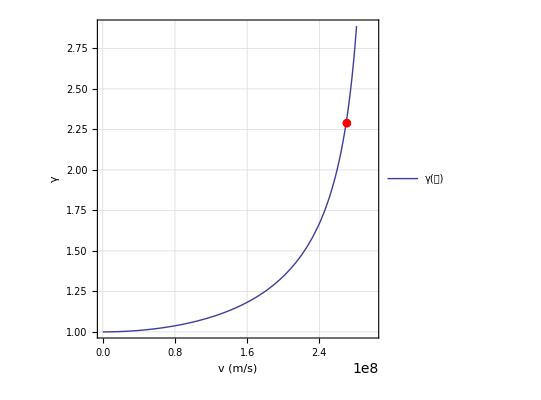

```mathematica
Show[γPlot1,γPlot2]
```